{-15.5/u[t]^2+3 u[t]+2 u''[t]==10}

{u[0]==1,u'[0]==0}

Solve::naqs: {-15.5/u[t]^2+3 u[t]+2 u''[t]==10} is not a quantified system of equations and inequalities.

Solve[{{-15.5/u[t]^2+3 u[t]+2 u''[t]==10}},{u}]

{{u→InterpolatingFunction[…]}}

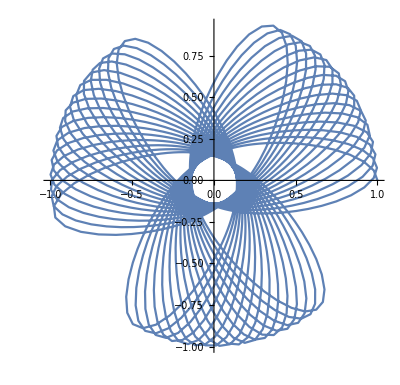

```mathematica
s={2u''[t]+3u[t]+-15.5/(u[t])^2==10}
ics= {u[0]==1,u'[0]==0}
sol=Solve[{s},{u}]
sol=NDSolve[{s,ics},{u},{t,-200,200}]

PolarPlot[Evaluate[1/u[t]/.sol,{t,0,200}]]
```

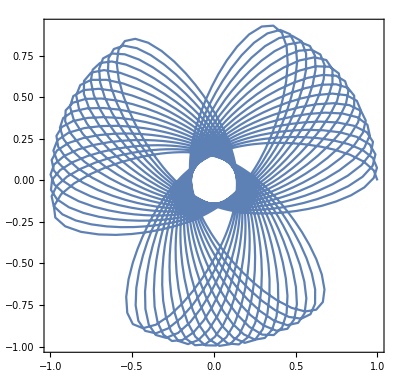

```mathematica
PolarPlot[Evaluate[1/u[t]/.sol,{t,0,200}],Frame->True,FrameStyle->Directive[GrayLevel[0,0.92],Thickness[Large]]]
```

```mathematica
PolarPlot[Evaluate[1/u[t]/.sol,{t,0,200}],Frame->True,FrameStyle->Directive[Black,Thickness[Large]]]
```

-Graphics-

{-1.5/u[t]^2+3 u[t]+u''[t]==0}

{u[0]==1,u'[0]==0}

Solve::naqs: {-1.5/u[t]^2+3 u[t]+u''[t]==0} is not a quantified system of equations and inequalities.

Solve[{{-1.5/u[t]^2+3 u[t]+u''[t]==0}},{u}]

{{u→InterpolatingFunction[…]}}

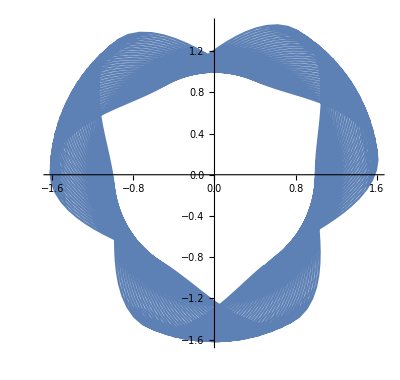

DSolve::ivar: {{1,-1,-1},{0,1,-1},{0,0,1}} is not a valid variable.

DSolve[{{1,-1,-1},{0,1,-1},{0,0,1}}[x]+{{1,-1,-1},{0,1,-1},{0,0,1}}'[x]==a Sin[x],{{1,-1,-1},{0,1,-1},{0,0,1}}[x],x]

```mathematica
s={u''[t]+3u[t]+-1.5/(u[t])^2==0}
ics= {u[0]==1,u'[0]==0}
sol=Solve[{s},{u}]
sol=NDSolve[{s,ics},{u},{t,-200,200}]

PolarPlot[Evaluate[1/u[t]/.sol,{t,0,200}]]

DSolve[y'[x]+y[x]==a Sin[x],y[x],x]
```

```mathematica
DSolve[y'[x]+y[x]==a Sin[x],y[x],x]
```

DSolve::ivar: {{1,-1,-1},{0,1,-1},{0,0,1}} is not a valid variable.

DSolve[{{1,-1,-1},{0,1,-1},{0,0,1}}[x]+{{1,-1,-1},{0,1,-1},{0,0,1}}'[x]==a Sin[x],{{1,-1,-1},{0,1,-1},{0,0,1}}[x],x]

```mathematica
DSolve[u''[t]+u[t]+a/(u[t])^2=0,u[t],t]
```

Set::write: Tag Plus in a/u[t]^2+u[t]+u''[t] is Protected.

DSolve::deqn: Equation or list of equations expected instead of 0 in the first argument 0.

DSolve[0,u[t],t]

```mathematica
DSolve[{u''[t]+u[t]=0},u[t],t]
```

Set::write: Tag Plus in u[t]+u''[t] is Protected.

DSolve::deqn: Equation or list of equations expected instead of 0 in the first argument {0}.

DSolve[{0},u[t],t]